# Binomial Probability Distribution

Binomial probability distributions are used in scenarios in which there are two acceptable outcomes.

## Conditions for a Binomial Distribution Experiment

A fixed number of trials

Each trial is independent

There are only two outcomes (success and failure)

The probability of each outcome remains constant in all trials

Binomial Probability Distribution Formula

P(x)=(n!)/((n-x)!x!)p^x q^(n-x)         for x=0,1,2,...,n
where
	n=number of trials
	x=number of successes in n trials
	p=probability of success in any one trial
	q=probaility of failure in any one trial

Flipping a coin is an example of a Binomial Probability Distribution. Let’s say we flip a coin twice, and when we get heads, we will consider the trial a success with a probability of .5, and when we get Tails we will treat the trial as a failure with a probability of 0.5. Since we flip the coin twice, we have 2 trials and four possible outcomes.

-Graphics-

Plot probabilities of  getting 0, 1, and 2 heads.

```mathematica
n=2; p=.5;
```

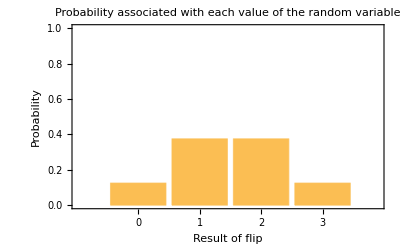

```mathematica
BarChart[Table[PDF[BinomialDistribution[n,p],i],{i,0,n}],PlotLabel->Style["Probability associated with each value of the random variable",Blue,12],Frame->True,FrameLabel->{"Result of flip","Probability"},ChartLabels->{Range[0,n]},PlotRange->{0,1}]
```

Based on frequency distribution, what is the probability of getting one or more heads? P(1)+P(2)

The interactive demonstration below allows you to explore the probability distribution for up to 20 coin tosses. When should you change the probability p? Explain.

```mathematica
Manipulate[
BarChart[Table[PDF[BinomialDistribution[n,p],i],{i,0,20}],
PlotRange->{{-.5,21.5},{-.1,.5}},
Epilog->{PointSize[.03],RGBColor[1,.47,0],Point[{n*p+1,0}]},
ImageSize->{450,350}],
{{n,20,"number of tosses n"},1,20,1,Appearance->"Labeled"},
{{p,.5,"probability p of head on each toss"},0,1,
Appearance->"Labeled"}
]
```

If a coin that comes up heads with probability  is tossed  times, the number of heads observed follows a binomial probability distribution. Move the sliders and watch how the distribution changes. The mean of the distribution—the number of heads one “expects” to observe—is marked with an orange circle on the horizontal axis.

Practice:
If you flip a fair coin 15 times, what is the probability you get the following:
1.  heads will appear exactly 7 times?
2.  there will be at most 7 heads?
3.  there will be at least 6 heads?  
4. heads will appear

Example 2: Are you thinking of getting a tattoo? Based in a Harris poll, among adults who regret getting tattoos, 20% say that they were too young when they got their tattoos. Assume that 5 adults who regret getting a tattoo are randomly selected, find the indicated probability:
1. Find the probability that none of the selected adults say that they were too young to get tattoos.
2. Find the probability that exactly one of the selected adults says that he or she was too young to get tattoos.
3. Find the probability that the number of selected adults say they were too young is at most 1.

Using the BinomialDistribution function in the Wolfram language, we can explore try different experiments by simply changing the n and p values.

```mathematica
n=5;
```

```mathematica
p=.20;
```

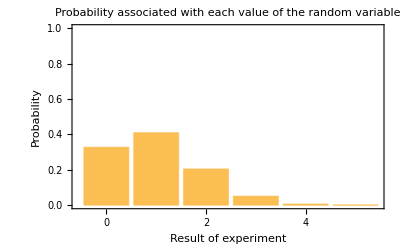

```mathematica
BarChart[Table[PDF[BinomialDistribution[n,p],i],{i,0,n}],PlotLabel->Style["Probability associated with each value of the random variable",Blue,12],Frame->True,FrameLabel->{"Result of experiment","Probability"},ChartLabels->{Range[0,n]},PlotRange->{0,1}]
```

Obtain probability distribution values

```mathematica
distValues=Table[{x, PDF[BinomialDistribution[n, p], x]}, {x, 0, n}]
```

{{0,0.32768},{1,0.4096},{2,0.2048},{3,0.0512},{4,0.0064},{5,0.00032}}

Creating a probability distribution table

```mathematica
TableForm@distValues
```

0 | 0.32768
1 | 0.4096
2 | 0.2048
3 | 0.0512
4 | 0.0064
5 | 0.00032

Getting a list of all the probabilities

```mathematica
prob=distValues[[All,2]]
```

{0.32768,0.4096,0.2048,0.0512,0.0064,0.00032}

Adding the probabilities of parts l1 to l2

```mathematica
n1=1; (*location of probability value*)
```

```mathematica
n2=2;
```

```mathematica
Total[prob[[n1;;n2]]]
```

0.73728

Answers to example 2

1. P(x=0)=0.3278
2. P(x=1)=0.4096
3. P(x⩽1)=P(x=0)+P(x=1) =0.7374

Practice

Let’s assume your have a friend who has a statistics quiz tomorrow, and he/she decides not to study for the quiz. The quiz consists of 10 multiple choice questions, and each question has 5 possible choices, but only one is the correct answer.
1. What is the probability your friend gets a perfect score on the quiz if he/she is just guessing the answers?
2. What is the probability he/she fails the exam? (70 is a passing grade and each question is worth 10 points
3. What would be your advice for you friend?

Further Explorations

Hypergeometric Probability Distribution

Authorship information

Silvani Vejar

07/03/2017

E.Vejar@Northeastern.edu

#### References

"Binomial Distribution" from the Wolfram Demonstrations Project
 http://demonstrations.wolfram.com/BinomialDistribution/
Contributed by: Chris Boucher

http://onlinestatbook.com

Elementary Statistics by Mario Triola